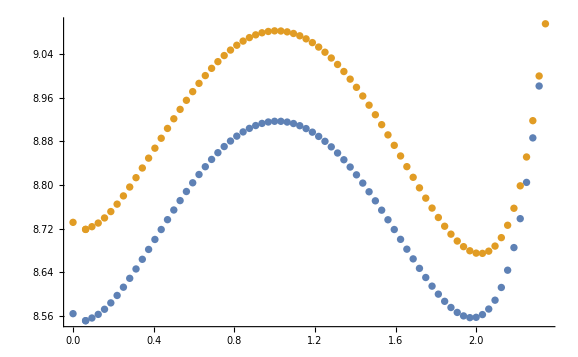

```mathematica
a={{0,8.564201},{0.062500,8.551287},{0.062500,8.551287},{0.093750,8.556258},{0.125000,8.562903},{0.156250,8.572267},{0.187500,8.583980},{0.218750,8.597599},{0.250000,8.612725},{0.281250,8.629010},{0.312500,8.646153},{0.343750,8.663893},{0.375000,8.681996},{0.406250,8.700259},{0.437500,8.718499},{0.468750,8.736551},{0.500000,8.754268},{0.531250,8.771519},{0.562500,8.788184},{0.593750,8.804156},{0.625000,8.819339},{0.656250,8.833647},{0.687500,8.847004},{0.718750,8.859341},{0.750000,8.870598},{0.781250,8.880724},{0.812500,8.889673},{0.843750,8.897405},{0.875000,8.903889},{0.906250,8.909099},{0.937500,8.913013},{0.968750,8.915616},{1.000000,8.916899},{1.031250,8.916857},{1.062500,8.915491},{1.093750,8.912806},{1.125000,8.908815},{1.156250,8.903533},{1.187500,8.896982},{1.218750,8.889191},{1.250000,8.880193},{1.281250,8.870028},{1.312500,8.858743},{1.343750,8.846392},{1.375000,8.833036},{1.406250,8.818745},{1.437500,8.803598},{1.468750,8.787682},{1.500000,8.771097},{1.531250,8.753953},{1.562500,8.736373},{1.593750,8.718492},{1.625000,8.700463},{1.656250,8.682455},{1.687500,8.664652},{1.718750,8.647264},{1.750000,8.630519},{1.781250,8.614674},{1.812500,8.600012},{1.843750,8.586849},{1.875000,8.575538},{1.906250,8.566475},{1.937500,8.560104},{1.968750,8.556927},{2.000000,8.557513},{2.031250,8.562516},{2.062500,8.572691},{2.093750,8.588918},{2.125000,8.612239},{2.156250,8.643893},{2.187500,8.685362},{2.218750,8.738387},{2.250000,8.804884},{2.281250,8.886463},{2.312500,8.981584}};
b={{0,8.731634},{0.062500,8.718715},{0.062500,8.718715},{0.093750,8.723686},{0.125000,8.730328},{0.156250,8.739688},{0.187500,8.751396},{0.218750,8.765009},{0.250000,8.780126},{0.281250,8.796402},{0.312500,8.813534},{0.343750,8.831259},{0.375000,8.849347},{0.406250,8.867591},{0.437500,8.885809},{0.468750,8.903836},{0.500000,8.921525},{0.531250,8.938743},{0.562500,8.955371},{0.593750,8.971301},{0.625000,8.986437},{0.656250,9.000691},{0.687500,9.013988},{0.718750,9.026257},{0.750000,9.037438},{0.781250,9.047479},{0.812500,9.056332},{0.843750,9.063957},{0.875000,9.070322},{0.906250,9.075398},{0.937500,9.079164},{0.968750,9.081602},{1.000000,9.082700},{1.031250,9.082453},{1.062500,9.080859},{1.093750,9.077921},{1.125000,9.073648},{1.156250,9.068054},{1.187500,9.061157},{1.218750,9.052982},{1.250000,9.043558},{1.281250,9.032921},{1.312500,9.021113},{1.343750,9.008183},{1.375000,8.994186},{1.406250,8.979186},{1.437500,8.963254},{1.468750,8.946471},{1.500000,8.928927},{1.531250,8.910723},{1.562500,8.891971},{1.593750,8.872796},{1.625000,8.853336},{1.656250,8.833747},{1.687500,8.814199},{1.718750,8.794881},{1.750000,8.776004},{1.781250,8.757801},{1.812500,8.740531},{1.843750,8.724483},{1.875000,8.709977},{1.906250,8.697371},{1.937500,8.687067},{1.968750,8.679514},{2.000000,8.675221},{2.031250,8.674767},{2.062500,8.678813},{2.093750,8.688126},{2.125000,8.703599},{2.156250,8.726287},{2.187500,8.757449},{2.218750,8.798588},{2.250000,8.851471},{2.281250,8.918047},{2.312500,8.999958},{2.343750,9.095665}};
ListPlot[{a,b}]
```

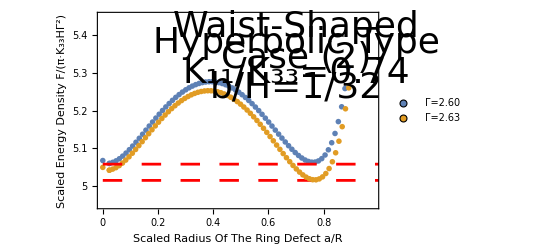

```mathematica
aa=a*Table[{1/2.6,4/2.6^2},{i,0,74}];
bb=b*Table[{1/2.63,4/2.63^2},{i,0,75}];
ListPlot[{aa,bb},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{5,5.1,5.2,5.3,5.4},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.98},{4.95,5.45}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Γ=2.60","Γ=2.63"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{{Red,Dashing[Large],Thickness[0.005],Line[{{0,5.058},{1,5.058}}]},{Red,Dashing[Large],Thickness[0.005],Line[{{0,5.015},{1,5.015}}]},
Text[Style["Waist-Shaped",Directive[Black,36]],{0.7,5.42}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.7,5.38}],Text[Style["Case (2)",Directive[Black,36]],{0.7,5.34}],Text[Style["K_11/K_33=0.74",Directive[Black,36]],{0.7,5.3}],Text[Style["b/H=1/32",Directive[Black,36]],{0.7,5.26}]}]
```

```mathematica
8.564201×4/2.6^2
```

5.06757

```mathematica
8.674767×4/2.63^2
```

5.01656